### Load package

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ian/Projects/nrmma

```mathematica
<<"Plotting.m"
```

### Test data

```mathematica
data1=Table[{x,Sin[2Pi x-Pi]},{x,0,1,0.01}];
```

```mathematica
data2=Table[{x,Sin[2Pi x-Pi/2]},{x,0,1,0.01}];
```

```mathematica
data3=Table[{x,Sin[2Pi x-Pi/1.5]},{x,0,1,0.01}];
```

### Documentation

ListLinePlotWithLegend[args...] is the same as ListLinePlot but it accepts additional options.  The default plot style is also modified to give different colours and slightly thicker lines.

PlotLegend -> {label1, label2, ...}
LegendPosition -> {xpos, ypos}

labelN are the labels to give to each curve
xpos is Left or Right
ypos is Top or Bottom

PresentationListLinePlot[args...] is the same as ListLinePlotWithLegend but the label style is set to Medium and a frame is added.

Notes and limitations:
PlotLegend must be given as a list, not a single value.
The list of curves to plot must be given in {{x,y},...} form rather than {{y1, y2...}, ...}, or the plot styles might not be consistent.

### Examples

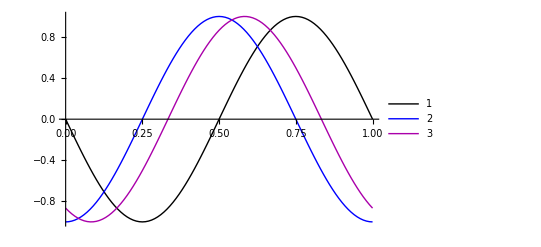

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3}]
```

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3},
LegendPosition->{Left,Bottom}]
```

-Graphics-

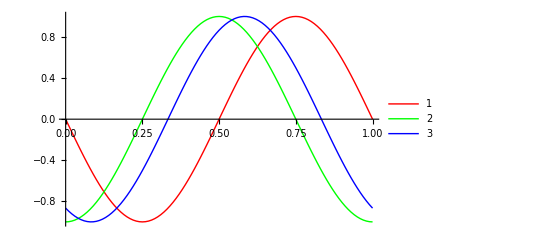

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3},
PlotStyle->{Red,Green,Blue}]
```

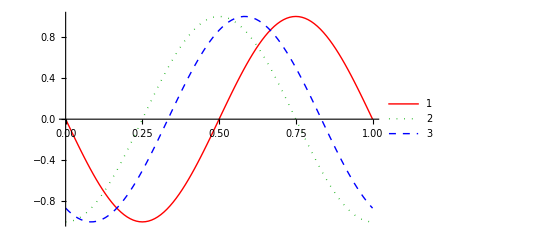

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3},
PlotStyle->{Red,Directive[Darker@Green,Dotted],Directive[Blue,Dashed]}]
```

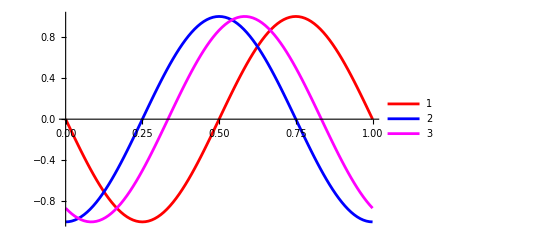

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3},
PlotStyle->
{Directive[AbsoluteThickness[2],Red],
Directive[AbsoluteThickness[2],Blue],
Directive[AbsoluteThickness[2],Magenta]}]
```

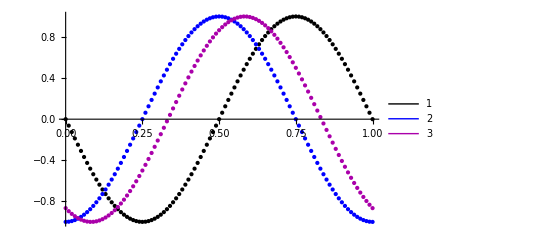

```mathematica
ListLinePlotWithLegend[
{data1,data2,data3},
PlotLegend->{1,2,3},
Joined->False]
```

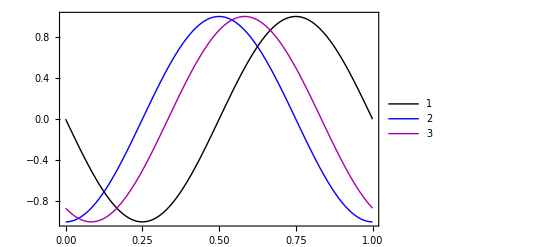

```mathematica
PresentationListLinePlot[
{data1,data2,data3},
PlotLegend->{1,2,3}]
```

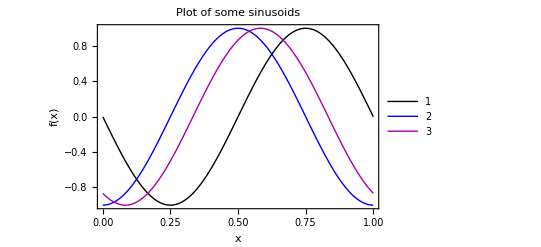

```mathematica
PresentationListLinePlot[
{data1,data2,data3},
PlotLegend->{1,2,3},
FrameLabel->{"x","f(x)"},
PlotLabel->"Plot of some sinusoids"]
```